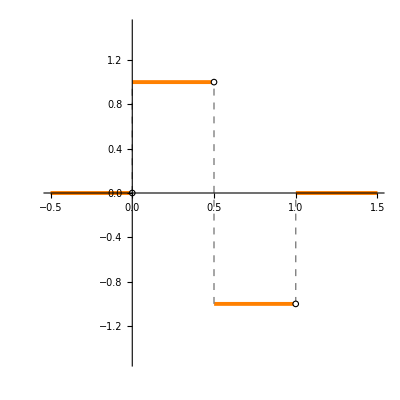

```mathematica
lv[x_, y1_, y2_] := Line[{{x, y1}, {x, y2}}]
R = 0.007;
(*Graphics[{
{Dashed, Line[{{1,0},{2,1},{3,0},{4,1},{5,0},{6,1}}]},
{}
}]*)
Plot[
Piecewise[{{1, 0≤ t < 0.5}, {-1, 0.5 ≤ t < 1}, {0, t < 0 || t ≥ 1}}], {t, -0.5, 1.5},
PlotStyle -> {Thickness ->R, Orange}, PlotRange -> {-1.5, 1.5},AspectRatio -> 1, Epilog -> {
{Dashed, Gray, lv[0, 0, 1]},
{Dashed, Gray, lv[0.5, -1, 1]},
{Dashed, Gray, lv[1, -1,0]},
{EdgeForm[Black],White,Disk[{0,0}, Offset[2]]},
{EdgeForm[Black],White,Disk[{0.5,1}, Offset[2]]},
{EdgeForm[Black],White,Disk[{1,-1}, Offset[2]]}
}]
```

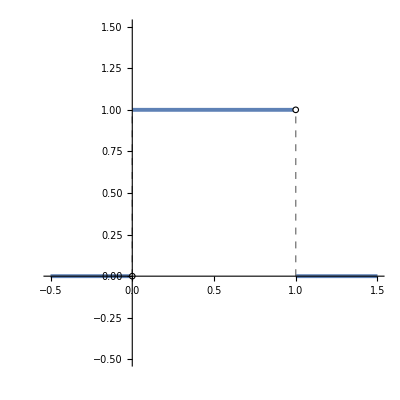

```mathematica
Plot[
Piecewise[{{1, 0≤ t < 1},{0, t < 0 || t ≥ 1}}], {t, -0.5, 1.5},
PlotStyle -> {Thickness -> R},AspectRatio -> 1, PlotRange -> {-0.5, 1.5}, Epilog -> {
{Dashed, Gray, lv[0, 0, 1]},
{Dashed, Gray, lv[1, 0, 1]},
{EdgeForm[Black],White,Disk[{1,1}, Offset[2]]},
{EdgeForm[Black],White,Disk[{0,0}, Offset[2]]}
}]
```

{Cos[π t],Cos[2 π t],Cos[3 π t]}

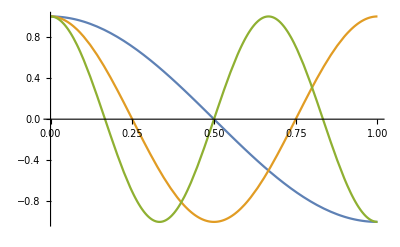

```mathematica
cs = Table[Cos[k π t], {k, 1, 3}]
Plot[cs, {t, 0, 1}]
```

Sin[8 t]

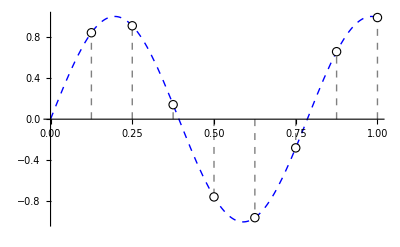

```mathematica
f[t_] = Sin[8 t]
d[x_] := {EdgeForm[Black],White,Disk[{x,f[x]}, Offset[3]]};
n = 8;
Ep = Join[Table[{Dashed, Gray, lv[k/n, 0, f[k/n]]}, {k, 1, n}], Table[d[k/n], {k, 1, n}]];
Plot[
f[t], {t, 0, 1},
PlotStyle -> {Thick, Blue, Dashed}, Epilog -> Ep]
```

```mathematica
(*{
{Dashed, Gray, lv[0, 0, 1]},
{Dashed, Gray, lv[1, 0, 1]},
d[0/4],
d[1/4],
d[2/4],
d[3/4],
d[4/4]
}*)
```

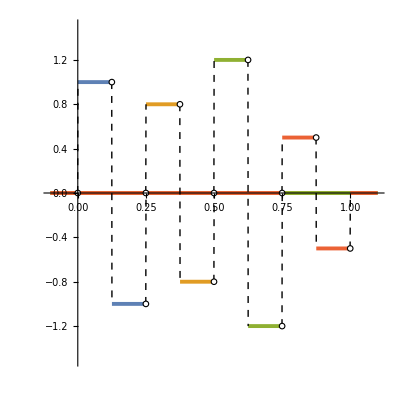

```mathematica
k = 2;
p = 1 / 2^k;
phi[t_, r_] := Piecewise[{{1, r p≤ t < (r+0.5) p}, {-1, (r+0.5) p ≤ t < (r+1) p}, {0, t < r p || t ≥ (r+1) p}}];
koefs = {1, 0.8, 1.2, 0.5};
plots = Table[koefs⟦i⟧ phi[t, i-1], {i, 1, 2^k}];
disk[x_, y_] := {EdgeForm[Black],White,Disk[{x,y}, Offset[2]]};
ln[x_, y1_, y2_] := {Dashed, Gray, lv[x, y1,y2]};
suka[x_, r_] := disk[x, koefs⟦r + 1⟧ phi[x - 1/10^3, r]];
L[x_, r_] := ln[x, 0, phi[x - 1/10^3, r]];
Ep = {
suka[0/8, 0],
suka[1/8, 0],
suka[2/8, 0],
suka[2/8, 1],
suka[3/8, 1],
suka[4/8, 1],
suka[4/8, 2],
suka[5/8, 2],
suka[6/8, 2],
suka[6/8, 3],
suka[7/8, 3],
suka[8/8, 3]
};
Plot[
plots, {t, -0.1, 1.1},
PlotStyle -> {Thickness -> R}, PlotRange -> {-1.5, 1.5},AspectRatio -> 1, ExclusionsStyle->Dashing[Small], Epilog -> Ep]
```

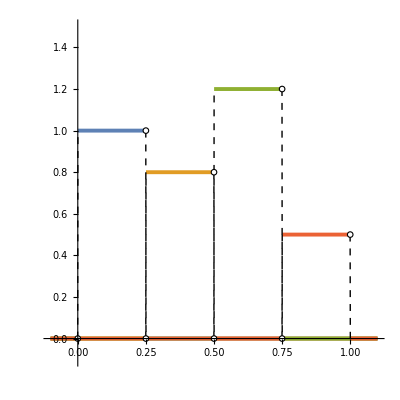

```mathematica
psi[t_, r_] := Piecewise[{{1, r p≤ t < (r+1) p}, {0, t < r p || t ≥ (r+1) p}}];
koefs = {1, 0.8, 1.2, 0.5};
plots = Table[koefs⟦i⟧ psi[t, i-1], {i, 1, 2^k}];
suka[x_, r_] := disk[x, koefs⟦r + 1⟧ psi[x - 1/10^3, r]];
Ep = {
suka[0/4, 0],
suka[1/4, 0],
suka[1/4, 1],
suka[2/4, 1],
suka[2/4, 2],
suka[3/4, 2],
suka[3/4, 3],
suka[4/4, 3]
};
Plot[
plots, {t, -0.1, 1.1},
PlotStyle -> {Thickness -> R}, PlotRange -> {-0.1, 1.5},AspectRatio -> 1, ExclusionsStyle->Dashing[Small], Epilog -> Ep]
```